```mathematica
Get["RootSearch`"]
```

```mathematica
?RootSearch
```

```mathematica
(*Data*)
nperiods =200;
μ=3.9877848 10^14;
Mp=1000;
l=50000;
a=6870000;
τ = 2*10^7;


period = 2 π √(a^3/μ);
ranget = nperiods*period;

psiQ =τ ;


(*Position vectorc and linear kinetic energy (translation of centre of mass)*)
rm[t] = ({{rc[t] Cos[θ[t]]}, {rc[t] Sin[θ[t]]}, {0}});
rp1[t]=rm[t]+({{l Cos[ψ[t]+θ[t]]}, {l  Sin[ψ[t]+θ[t]]}, {0}});
rp2[t]=rm[t]-({{l Cos[ψ[t]+θ[t]]}, {l  Sin[ψ[t]+θ[t]]}, {0}});

rm'[t]=D[rm[t], t];
rp1'[t]=D[rp1[t], t];
rp2'[t]=D[rp2[t], t];

Subscript[T, lin]=1/2 (2*Mp) (rc'[t]^2+rc[t]^2 θ'[t]^2);

(*Rotational kinetic energy (rotation of system about centre of mass)*)
ω[t]=({{0}, {0}, {(θ'[t]+ψ'[t])}});

Subscript[ⅈ, 123]=({{0, 0, 0}, {0, 2 Mp l^2, 0}, {0, 0, 2 Mp l^2}});

Subscript[T, rot]=1/2 Transpose[ω[t]].Subscript[ⅈ, 123].ω[t];

T=Subscript[T, lin]+Subscript[T, rot];

(*potential energy*)
Subscript[U, p1]=-(μ Mp)/(√(Transpose[rp1[t]].rp1[t]));
Subscript[U, p2]=-(μ Mp)/(√(Transpose[rp2[t]].rp2[t]));
V=Subscript[U, p1]+Subscript[U, p2];

L=T-V;
eqn1=Simplify[D[D[L, ψ'[t]], t]-D[L, ψ[t]]-psiQ];
eqn2 = Simplify[D[D[L, θ'[t]], t]-D[L, θ[t]]];
eqn3 = Simplify[D[D[L, rc'[t]], t]-D[L, rc[t]]];
```

```mathematica
systemfunc[e_]:=(

psi0 = 0;
psidsh0 =0;

r0 = a (1-e);
rdsh0 = 0;

theta0 = 0;
thetadsh0=1/r0*√((μ (1+e))/(a (1-e)))  ;

system=NDSolve[{eqn1==0,eqn2==0,eqn3==0,
ψ[0]==psi0,ψ'[0]==psidsh0, θ[0] == theta0,θ'[0]==thetadsh0,rc[0] == r0,rc'[0]==0},
{ψ,θ,rc},{t,0,ranget},
MaxSteps->∞,AccuracyGoal->Automatic];
psis[t_]:=ψ[t]/.system[[1]];
psidhs[t_]:=ψ'[t]/.system[[1]];
rvs[t_] :=rc'[t]/.system[[1]];
as[t_]:=rc''[t]/.system[[1]];
rs[t_]:=rc[t]/.system[[1]];
thetas[t_]:=θ[t]/.system[[1]]

)
```

```mathematica
stddevs = {};
coofmean = {};
apogeegees={};
frames = {};

Do[Print[eee];
systemfunc[eee];
rootst = {};
Do[rootst = Append[rootst,RootSearch[rvs[t]==0,{t,period*n,(n+30)*period}]],{n,0,nperiods-30,30}];
rootst = Flatten[rootst];
roots = {};
Do[roots = Append[roots,t/.rootst[[n]]],{n,1,Length[rootst]}];
rvals = {};
apogees = {};
Do[rvals=Append[rvals,{roots[[n]],rs[roots[[n]]]}],{n,1,Length[roots]}];
datas =FindClusters[rvals[[All,2]],2];
cluster1mean = Mean[datas[[1]]];
cluster2mean = Mean[datas[[2]]];
If[cluster1mean>cluster2mean,apogees = datas[[1]];perigees=datas[[2]],apogees=datas[[2]];perigees=datas[[1]]];
stddevs = Append[stddevs,StandardDeviation[apogees]];
frames = Append[frames,ListPlot[{apogees,perigees},PlotMarkers->{•,15},PlotLabel->Style["Apogee/Perigee Clusters",FontFamily->"Liberation Serif",35],AxesLabel->{Style[" ",FontFamily->"Liberation Serif"],Style["r",FontFamily->"Liberation Serif"]},LabelStyle->Directive[Black,18,FontFamily->"Liberation Serif"],ImageSize->{720}]];
coofmean= Append[coofmean,{eee,StandardDeviation[apogees]/Mean[apogees]}],
{eee,0.3,0.3,0.05}]
```

0.3

$MinPrecision::precset: Cannot set $MinPrecision to -∞; value must be a non-negative number or Infinity.

General::stop: Further output of $MinPrecision::precset will be suppressed during this calculation.

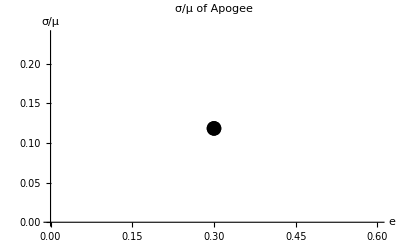

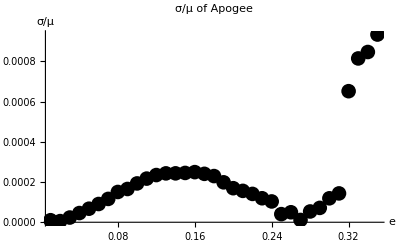

Part::partw: Part 75 of {} does not exist.

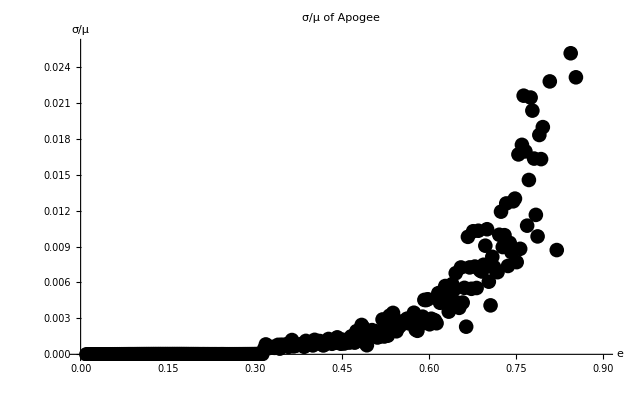

```mathematica
Manipulate[frames[[n]],{n,1,Length[frames],1}]
ListPlot[coofmean[[1;;-1]],PlotMarkers->{•,15},PlotLabel->Style["σ/μ of Apogee",FontFamily->"Liberation Serif",35],AxesLabel->{Style["e",FontFamily->"Liberation Serif"],Style["σ/μ",FontFamily->"Liberation Serif"]},LabelStyle->Directive[Black,18,FontFamily->"Liberation Serif"],ImageSize->{1080},PlotRange->All,PlotStyle->Black]
```

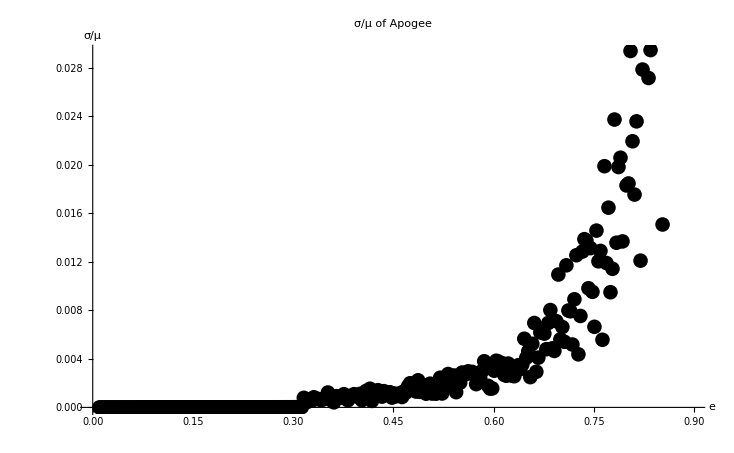

Part::partw: Part 297 of … does not exist.

```mathematica
ListPlot[coofmean,PlotMarkers->{•,15},PlotLabel->Style["σ/μ of Apogee",FontFamily->"Liberation Serif",35],AxesLabel->{Style["e",FontFamily->"Liberation Serif"],Style["σ/μ",FontFamily->"Liberation Serif"]},LabelStyle->Directive[Black,18,FontFamily->"Liberation Serif"],ImageSize->{1080},PlotStyle->Black]
```

```mathematica
clusters = {}
Do[clusters = Append[clusters, FindClusters[allpoints[[n]],2]],{n,1,Length[allpoints]}]
```

{}

```mathematica
means = {};
Do[means = Append[means, {Mean[clusters[[n]][[1]]],Mean[clusters[[n]][[2]]]}],{n,1,Length[clusters]}]
```

```mathematica
apos = {};
Do[If[means[[n]][[1]]>means[[n]][[2]],apos= Append[apos,clusters[[n]][[1]]],apos= Append[apos,clusters[[n]][[2]]]],{n,1,Length[clusters]}]
```

```mathematica
means
```

{{7.55469×10^6,6.18295×10^6},{8.24135×10^6,5.49575×10^6},{8.92764×10^6,4.80881×10^6},{4.12488×10^6,9.58822×10^6},{3.43706×10^6,1.02814×10^7},{2.75046×10^6,1.09482×10^7},{2.06393×10^6,1.16005×10^7},{1.37829×10^6,1.20113×10^7},{1.12879×10^7,692198.}}

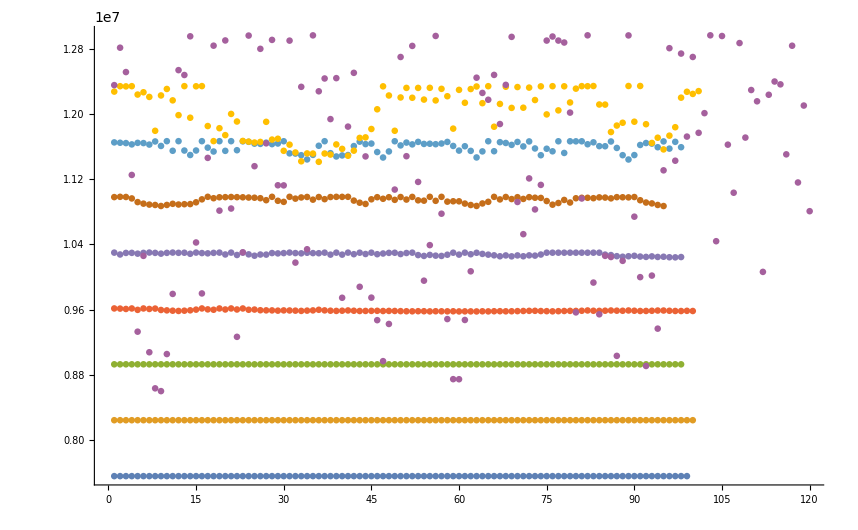

```mathematica
ListPlot[apos]
```

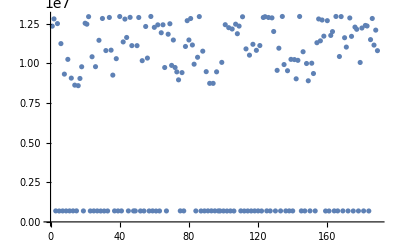

```mathematica
ListPlot[allpoints[[9]]]
```